### The basic example of the classic ‘drunk’ model in 2D situation:

P.S.: To be more specific, it must be mentioned that when we call “classic ‘drunk’ model” we are referring to a setting that the ‘drunk’ - or simply saying the point- has a fixed step length of 1.

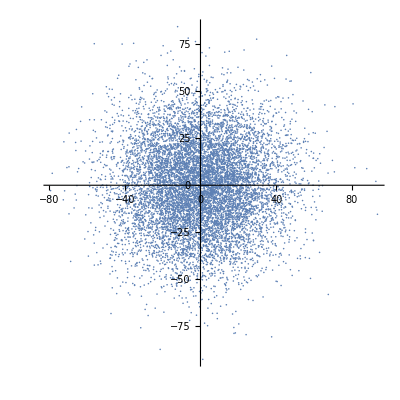

```mathematica
steps=1000;
times=10000;
list={{0,0}};
Do[angle=Table[RandomReal[{0,2 π}],steps];
position={Total[Cos[angle]],Total[Sin[angle]]};
list=Append[list,position],times];
ListPlot[list,PlotRange->All,AspectRatio->1]
```

### The codes and the chart below shows the general state of point’s distance from the center point:

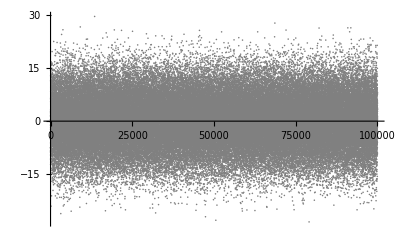

```mathematica
steps=100;
times=100000;
initial=Table[0,times];
Do[initial=initial+Cos[RandomReal[{0,2Pi},times]],steps];
ListPlot[initial,PlotStyle->Gray]
```

The codes below are trying to get the relation between tally and distance, while the lines are for possible fit.

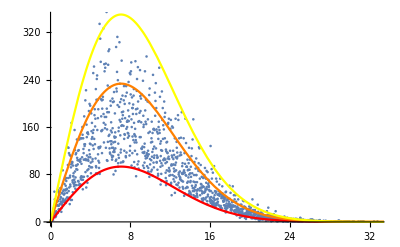

```mathematica
steps=100;
times=100000;
list={};
Do[angle=Table[RandomReal[{0,2Pi}],steps];
position={Total[Cos[angle]],Total[Sin[angle]]};
list=Append[list,√Total[position^2]],times];
Show[ListPlot[Tally[SetAccuracy[list,2]]],
Plot[80E*(x/(√steps))*E^(-(x^2/steps)),{x,0,35},PlotStyle->Red,PlotRange->All],
Plot[200E*(x/(√steps))*E^(-(x^2/steps)),{x,0,35},PlotStyle->Orange,PlotRange->All],
Plot[300E*(x/(√steps))*E^(-(x^2/steps)),{x,0,35},PlotStyle->Yellow,PlotRange->All]
]
```

From the graph compared with the initial simulation of the 2D ‘drunk’ model, it might lead to a perplex that it does not match our first instinct that the center point should be where the points are located most, but of course it is not that true. To have a better understanding of such a ‘hallucination’, here I also do a simple simulation, where any position in a circle with a radius of 1 has the same chance to have a point shown. Also the further interpretation of this will be mentioned later.

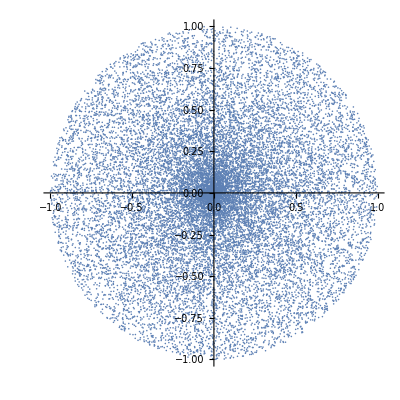

```mathematica
steps=1;
times=20000;
list={{0,0}};
Do[angle=Table[RandomReal[{0,2 π}],steps];
length=Table[RandomReal[{0,1}],steps];
position={Total[length*Cos[angle]],Total[length*Sin[angle]]};list=Append[list,position],times];
ListPlot[list,PlotRange->All,AspectRatio->1]
```

### Below might be the original version of the all classic ‘drunk’ model.

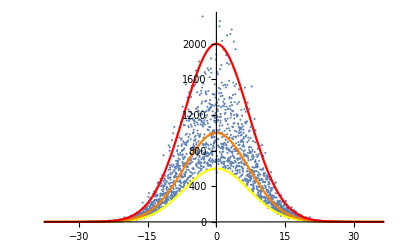

```mathematica
steps=100;
times=1000000;
initial=Table[0,times];
Do[initial=initial+Cos[RandomReal[{0,2Pi},times]],steps];
Show[ListPlot[Tally[SetAccuracy[initial,2]]],
Plot[600 E^(-(x/(√steps))^2),{x,-steps,steps},PlotStyle->Yellow,PlotRange->All],
Plot[1000 E^(-(x/(√steps))^2),{x,-steps,steps},PlotStyle->Orange,PlotRange->All],
Plot[2000 E^(-(x/(√steps))^2),{x,-steps,steps},PlotStyle->Red,PlotRange->All]
]
```

BUT it isn’t for all situations. The exceptions lie in the simulations having few steps:

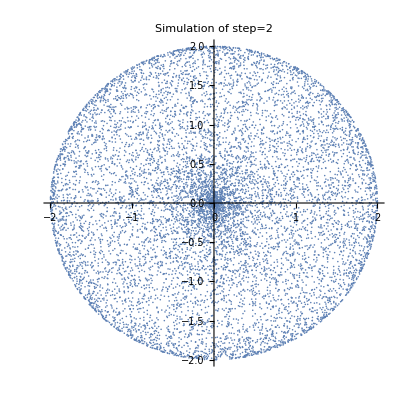

```mathematica
steps=2;
times=10000;
list={{0,0}};
Do[angle=Table[RandomReal[{0,2 π}],steps];
position={Total[Cos[angle]],Total[Sin[angle]]};
list=Append[list,position],times];
ListPlot[list,PlotRange->All,AspectRatio->1,PlotLabel->Style["Simulation of step=2",18,Black]]
```

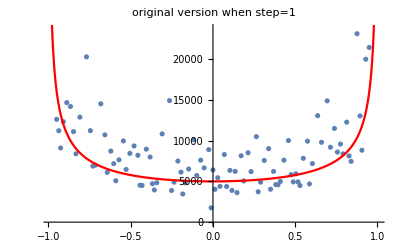

```mathematica
steps=1;
times=1000000;
initial=Table[0,times];
Do[initial=initial+Cos[RandomReal[{0,2Pi},times]],steps];
Show[ListPlot[Tally[SetAccuracy[initial,2]],PlotLabel->Style[
"original version when step=1",
18,Black]],
Plot[5000/(√(1-x^2)),{x,-1,1},PlotRange->All,PlotStyle->Red]]
```

They are very interesting exceptions, which will be partially explained in the later sections.

#### Here is my mathematical formula for the original model:

```mathematica
f[n_Integer,x_]:=Integrate[f[n-1,t]*1/(√(1-(x-t)^2)),{t,x-1,x+1}]
f[1,x_]:=1/(√(1-x^2))/;-1<x<1;
f[1,x_]:=0/;x≤-1∨x≥1
```

Or in natural writing form:

F[1,x]=1/(√(1-x^2)), -1<x<1
               =0 , x≤-1∨x≥1
F[n,x]=∫_(x-1)^(x+1) F[n-1,t]*dt/(√(1-(x-t)^2))
Which I nor the computer can solve it.

## In 3D situation:

```mathematica
steps=1000;
times=10000;
list={{0,0,0}};
Do[angle1=Table[RandomReal[{0,2Pi}],steps];
angle2=Table[RandomReal[{0,2Pi}],steps];
position=
{Total[Cos[angle1]Cos[angle2]],
Total[Cos[angle1]Sin[angle2]],
Total[Sin[angle2]]};
list=Append[list,position],times];
Graphics3D[{PointSize[Small],Black,Point[list]},AspectRatio->1]
```

-Graphics3D-

#### Below shows the tally-distance graph of the situation simulated:

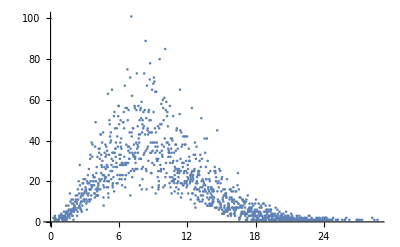

```mathematica
steps=100;
times=20000;
list={};
Do[angle1=Table[RandomReal[{0,2Pi}],steps];
angle2=Table[RandomReal[{0,2Pi}],steps];
position=
{Total[Cos[angle1]Cos[angle2]],
Total[Cos[angle1]Sin[angle2]],
Total[Sin[angle2]]};
list=Append[list,Sqrt[Total[position^2]]],times];
ListPlot[Tally[SetAccuracy[list,2]]]
```

## Non-traditional ‘drunk’ model:

By non-traditional ‘drunk’ model, I refer to a situation where the point have certain steps, each of which has a random length between 0 and 1 and a random angle.

#### Simulation:

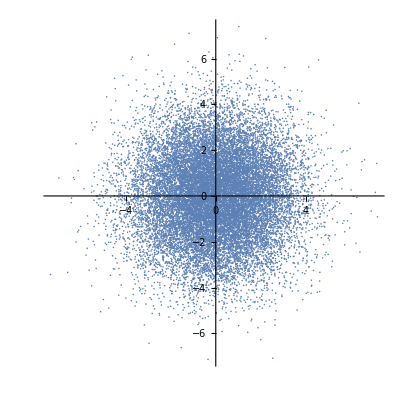

```mathematica
steps=20;
times=20000;
list={{0,0}};
Do[angle=Table[RandomReal[{0,2 π}],steps];
length=Table[RandomReal[{0,1}],steps];
position={Total[length*Cos[angle]],Total[length*Sin[angle]]};list=Append[list,position],times];
ListPlot[list,PlotRange->All,AspectRatio->1]
```

#### Tally-distance graph:

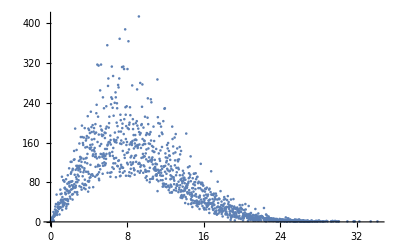

```mathematica
Clear[x,angle,position];
steps=100;
times=100000;
angle:=Table[RandomReal[{0,2Pi}],steps];
position[x_]:={Total[Cos[x]],Total[Sin[x]]};
distance[x_]:=Sqrt[Total[position[x]^2]];
list=Table[distance[angle],times];
ListPlot[Tally[SetAccuracy[list,2]]]
```

#### Below show the fits I tried, in the codes of which % means the graph above:

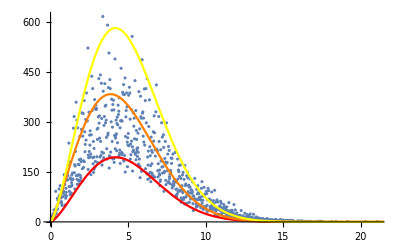

```mathematica
Show[%,
Plot[200*((2x)^1.4/(√steps))*E^(-((2x)^2/steps)),{x,0,35},PlotStyle->Red,PlotRange->All],
Plot[600*((2x)^1.2/(√steps))*E^(-((2x)^2/steps)),{x,0,35},PlotStyle->Orange,PlotRange->All],
Plot[600*((2x)^1.4/(√steps))*E^(-((2x)^2/steps)),{x,0,35},PlotStyle->Yellow,PlotRange->All]
]
```

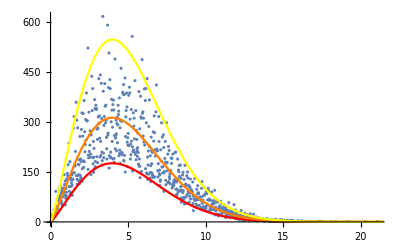

```mathematica
Show[%38,
Plot[450*((2x)/(√steps))^1.2*E^(-((2x)/(√steps))^1.8),{x,0,35},PlotStyle->Red,PlotRange->All],
Plot[800*((2x)/(√steps))^1.2*E^(-((2x)/(√steps))^1.8),{x,0,35},PlotStyle->Orange,PlotRange->All],
Plot[1400*((2x)/(√steps))^1.2*E^(-((2x)/(√steps))^1.8),{x,0,35},PlotStyle->Yellow,PlotRange->All]

]
```

To my astonishment, however, is that the simulation still resembles the basic model, which greatly stimulates my curiosity upon normal distribution. Thanks to TCC’s reminder, there is quite a wide variety of the models of normal distribution, He pointed out that ‘the accumulation of the random affairs can lead to normal distribution’, which can be indicated by the simulations listed below.

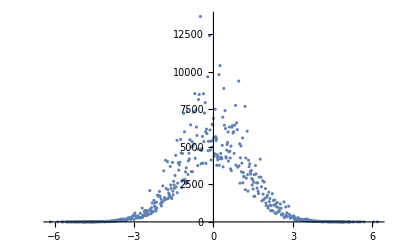

```mathematica
steps=10;
times=1000000;
initial=Table[0,times];
Do[initial=initial+Table[Power[RandomReal[{-1,1}],3],times],steps];
Show[ListPlot[Tally[SetAccuracy[initial,2]]]]
```

The graph above shows the simulation if the point has steps according to ‘x^3 distribution’, where x is a random real number between -1 and 1.

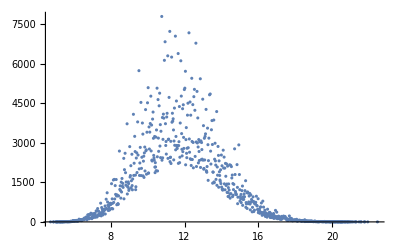

```mathematica
steps=10;
times=1000000;
initial=Table[0,times];
Do[initial=initial+Table[Exp[RandomReal[{-1,1}]],times],steps];
Show[ListPlot[Tally[SetAccuracy[initial,2]]]]
```

This is the exponential type, or e^x,where x is a random real number between -1 and 1. It also shows a glimpse of standard distribution.

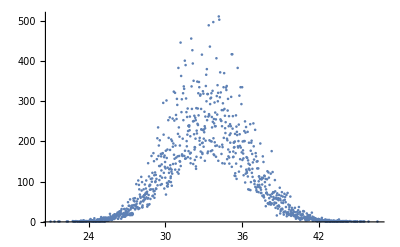

```mathematica
steps=100;
times=100000;
initial=Table[0,times];
Do[initial=initial+Table[Power[RandomReal[{-1,1}],2],times],steps];
Show[ListPlot[Tally[SetAccuracy[initial,2]]]]
```

The Log version:

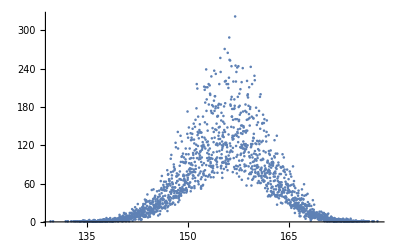

```mathematica
steps=100;
times=100000;
initial=Table[0,times];
Do[initial=initial+Table[Log[RandomReal[{1,10}]],times],steps];
Show[ListPlot[Tally[SetAccuracy[initial,2]]]]
```

#### In any simulation there always show a similar type of standard distribution, though there is a need to mention that they doesn’t perfectly fit the distribution, mainly due to the reason that these simulations all have a range of the distance, while the standard distribution does not. Indeed, these have made the TCC’s words intelligible, but they also popped up my question about how these appear like this, for which I need a mathematical explanation.